```mathematica
A=6.936659173135963*10^39; 
B=6703132746196289 ;
n=5 ;
m=3;
f[x_]:=A x^n Exp[-B*x^m];
```

```mathematica
Ψ[t_] := Tanh[π/2 Sinh[t]];
φ[t_]:=ArcSinh[Log[(1+t)/(1-t)]/π];
j[t_]:=1/(5*10^-6-1-t) + 1;
```

```mathematica
g[t_]:=f[Ψ[t]]*Ψ'[t]
h[t_]:=f[φ[t]]*φ'[t]
J[t_]:=f[j[t]]*j'[t]
ff[t_]:=InverseFunction[f][t]
Limit[j[t],t->5*10^-6]
```

0

General::munfl: Exp[-53020.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.27173×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.63408×10^14] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

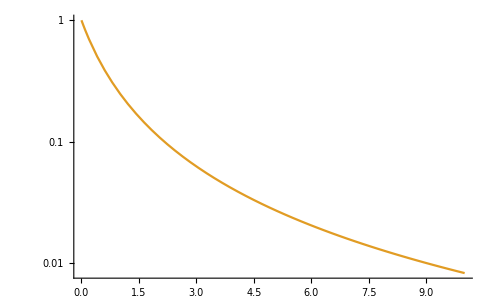

```mathematica
(*Plot[h[t],{t,0,10^-4},PlotRange->All]*)
LogPlot[{f[j[t]],j'[t]},{t,0,10},PlotRange->All]
```

```mathematica
h[0.001]
```

General::munfl: Exp[-1.72949×10^6] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
hh=5*10^-6/100//N
```

5.×10^-8

```mathematica
5*10^-6/hh
```

100.

```mathematica
Sum[hh h[i*hh] ,{i,0,700,1}]//N
```

5.14604×10^7

```mathematica
Sum[hh g[i*hh] ,{i,10,50,1}]//N
```

3.42121×10^6

```mathematica
NIntegrate[f[tt],{tt,5*10^-6,10^-3}]
```

4.09168×10^7

```mathematica
2^-126//N
```

1.17549×10^-38